```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
ComplexAnalysis`BranchPoints[√(z^2-1),z]
ComplexAnalysis`BranchCuts[√(z^2-1),z]
```

{-1,1,ComplexInfinity}

(-1<Re[z]<0&&Im[z]==0)||Re[z]==0||(0<Re[z]<1&&Im[z]==0)

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes CAN

tmp

## temp

### Definition / Theorem

#### Example

Complex Integration

## Contour Integral

### Definition / Theorem

#### Example

```mathematica
cContourIntegral[1/z,z,path[4]]//Expand
```

2 ⅈ π

Visualizations

## Visualize Function

## Test-0

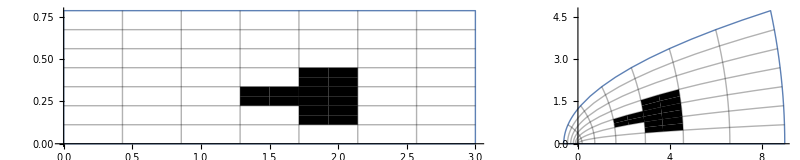

```mathematica
ClearAll[t1,t2,r1,r2,dt,dr]
F[z_]:=z^2;
t1=0;
t2=Pi/4;
r1=0;
r2=3;
GraphicsRow[
With[{z=r + I t,col=Black},
ParametricPlot[ReIm@#[z],{r,r1,r2},{t,t1,t2},
Mesh->6,
MeshShading->ArrayPad[{{None,col},{col,col},{None,col}},{{1,5},{3,5}},None],
Frame->False,
AxesOrigin->{0,0}]]&/@{Identity,F}]
```

## Test-1

```mathematica
f[s_]:=s
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{x,0,4},{y,0,8}]
]&/@{Identity,f}]
```

-Graphics-

## Test-2

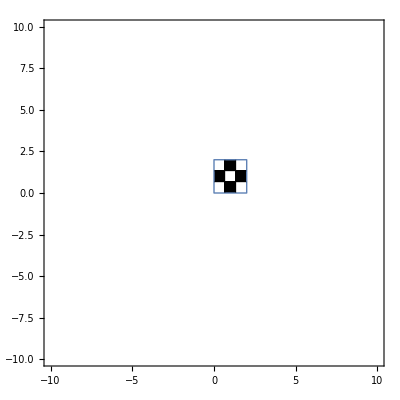

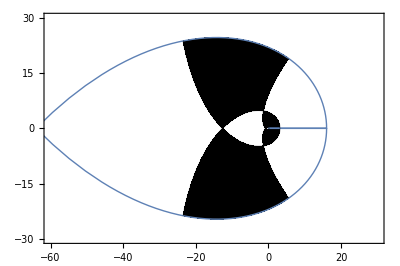

```mathematica
With[{s=σ+I t},
ParametricPlot[ReIm[s],{σ,0,2},{t,0,2},
Mesh->{2,2},
MeshShading->ArrayPad[{{None,Black},{Black,None}},{{0,0},{0,0}},None],
PlotRange->{{-10,10},{-10,10}}]
]
With[{s=σ+I t},
ParametricPlot[ReIm[s^4],{σ,0,2},{t,0,2},
Mesh->{2,2},
MeshShading->ArrayPad[{{None,Black},{Black,None}},{{0,0},{0,0}},None],
PlotRange->{{-60,30},{-30,30}}]
]
```

## tmp

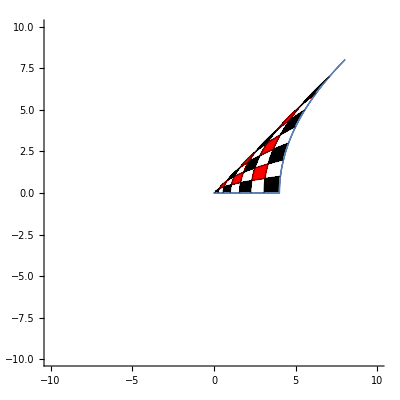

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[{σ^2+t^2,2σ t},{σ,0,2},{t,0,2},
Frame->False,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-10,10},{-10,10}}]
]&/@{Identity}]
```

```mathematica
(z-I Im[z])^2-(-I z+ I Re[z])^2+2I (z-I Im[z])(-I z+ I Re[z])//FullSimplify
```

z^2

```mathematica
((z-I Im[z])^2+(-I z+ I Re[z])^2+2I (z-I Im[z])(-I z+ I Re[z])//FullSimplify)/.z:>"#"
```

1/2 (#^2+2 # Conjugate[#]-Conjugate[#]^2)

```mathematica
(z-I Im[z])^2-(-I z+ I Re[z])^2-2I (z-I Im[z])(-I z+ I Re[z])//FullSimplify
```

Conjugate[z]^2

```mathematica
D[ComplexExpand[Re[(x+I y)^2]],{x,1}]
D[ComplexExpand[Im[(x+I y)^2]],{y,1}]
D[ComplexExpand[Re[(x+I y)^2]],{y,1}]
-D[ComplexExpand[Im[(x+I y)^2]],{x,1}]
```

2 x

2 x

-2 y

-2 y

```mathematica
D[ComplexExpand[Re[Conjugate[(x+I y)]^2]],{x,1}]
D[ComplexExpand[Im[Conjugate[(x+I y)]^2]],{y,1}]
D[ComplexExpand[Re[Conjugate[(x+I y)]^2]],{y,1}]
-D[ComplexExpand[Im[Conjugate[(x+I y)]^2]],{x,1}]
```

2 x

-2 x

-2 y

2 y

## Test-3

### Demo-1

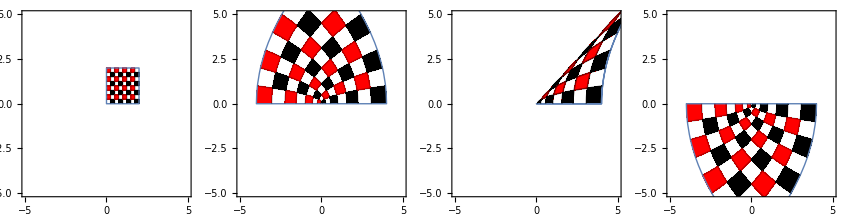

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,0,2},{t,0,2},
Axes->{True,True},
Frame->True,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,#^2&,1/2 (#^2+2 # Conjugate[#]-Conjugate[#]^2)&,Conjugate[#]^2&}]
```

### Demo-2

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,0,1},{t,0,1},
Axes->{True,True},
Frame->True,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,WeierstrassP[#,{0,1}]&,WeierstrassP[#,{1,0}]&}]
```

### Problem-1: Weierstrass-p is an even function : How to explain the following graphs below

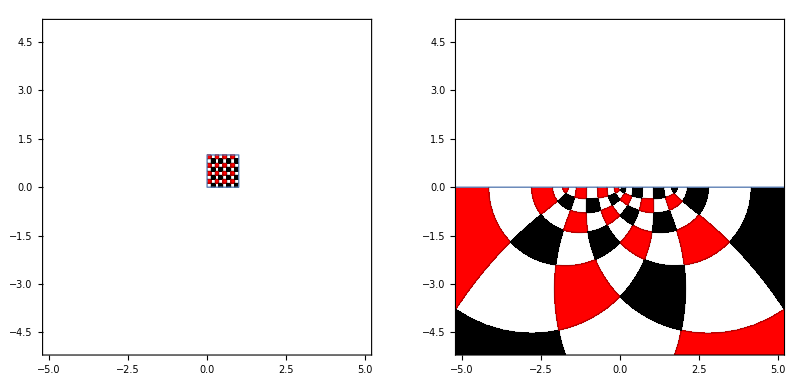

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,0,1},{t,0,1},
Axes->{True,True},
Frame->True,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,WeierstrassP[#,WeierstrassInvariants[{1,I}]]&}]
```

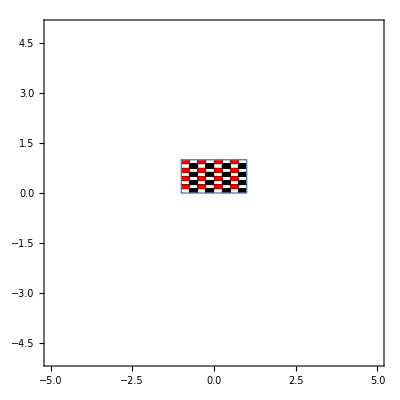

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,-1,1},{t,0,1},
Axes->{True,True},
Frame->True,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,WeierstrassP[#,WeierstrassInvariants[{1,I}]]&}]
```

```mathematica
ComplexPlot3D[WeierstrassP[z,WeierstrassInvariants[{1,I}]],{z,0,3+3I},PlotLegends->Automatic]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ)^2 encountered.

-Graphics3D-

```mathematica
WeierstrassInvariants[{1,I}]//N
```

{11.817+0. ⅈ,2.15808×10^-15+0. ⅈ}